## SpaRTaNS Examples: SO3 Cube Periodic-Diffusive-Absorbing

## Last updated: 04/30/2022

## Material Properties

Source Code

```mathematica
projectionOperator[vector_]:=IdentityMatrix[Length[vector]]-KroneckerProduct[vector,vector]

meanLifetime[sMC_]:=Mean[1/divideByZeroGivesZero[Diagonal[sMC]]]
divideByZeroGivesZero=Chop[#]/. 0|0. ->∞&;
numberOfStates=48;
```

```mathematica
Clear[isotropicScatteringMatricesSymmetric3D]
isotropicScatteringMatricesSymmetric3D[n_]:=Block[{angles,velocityProjection,normalizedEnergy,energyProjection,kpts,vels,sm,smVelocityRelaxed,smVelocityProjected},
kpts=N[SpherePoints[n]];
vels=N[SpherePoints[n]];

velocityProjection=Dot@@projectionOperator/@Orthogonalize[Prepend[Transpose[vels],ConstantArray[1,n]],Method->"GramSchmidt"];
normalizedEnergy=ConstantArray[1/√n,n];
energyProjection=projectionOperator[normalizedEnergy];

sm=Normal[SparseArray[{i_,i_}:>n-1.,{n,n},-1.]/n];

smVelocityRelaxed=energyProjection.DiagonalMatrix[Diagonal[sm]].energyProjection;
smVelocityProjected=velocityProjection.sm.velocityProjection;

{kpts,vels,sm,smVelocityProjected,smVelocityRelaxed}

]

scaledIsotropicScatteringMatrix3D[m_][{τMC_,∞}]:=Block[{kpts,vels,numeric,sMC,sMR,β,α},
{kpts,vels,numeric,sMC,sMR}=isotropicScatteringMatricesSymmetric3D[m];
α=1/τMC meanLifetime[sMC];
{kpts,vels,numeric,sMC,sMR,α sMC}

]
```

Material Properties

We will consider a 3D isotropic material (SO3)

Using a 48 states discretization

We will consider a material in the “Hydrodynamic” Regime

l_MC/W ~ 0.2, l_MR/W → ∞

The group velocities and scattering matrix are plotted below

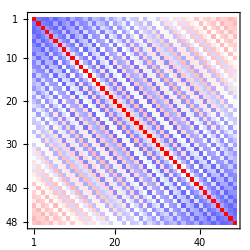
-Graphics3D- | -Graphics-

```mathematica
{kpts["SO3"],vels["SO3"],numeric["SO3"],smMomentumConserving["SO3"],smMomentumRelaxing["SO3"],sm["SO3"]}=scaledIsotropicScatteringMatrix3D[numberOfStates][{100,∞}];

With[{cf=(Blend[{Blue,White,Red},#]&)},
Multicolumn[{Graphics3D[{{Opacity[0.5],Arrow[{{0,0,0},#}]&/@vels["SO3"]}},ImageSize->250],
MatrixPlot[sm["SO3"],PlotLegends->LinearGradientImage[{Bottom,Top}->cf,{30,300}],ImageSize->250,ColorFunction->cf]
},2]]
```

We split the scattering matrix into diagonal and mixing-matrix components

```mathematica
diagonal["SO3"]=Diagonal[sm["SO3"]];
mixingMatrix["SO3"]=sm["SO3"]-DiagonalMatrix[diagonal["SO3"]];
frequencies["SO3"]=ConstantArray[1.,numberOfStates];
velocities["SO3"]=vels["SO3"]//N;
```

## Mesh Properties

Source Code

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
visualizeMesh[mesh_]:=With[{n=Length[mesh["BoundaryElementMarkerUnion"]]},
Echo[ColorData["BrightBands"]/@Rest[Subdivide[n]]];
mesh["Wireframe"[
"MeshElementStyle"->Directive@@@Thread[{FaceForm@*ColorData["BrightBands"]/@Rest[Subdivide[n]],EdgeForm[None]}],
Lighting->"Neutral",
Axes->True,Boxed->True,AxesLabel->{"x","y","z"}]]
]
```

Built-in Mesh

```mathematica
hexmesh["SO3"]["cube-periodic"]=ToElementMesh[Cuboid[{-500,-500,-500},{500,500,500}],"MeshOrder"->1,MaxCellMeasure->{"Volume"->100^3}];
mesh["SO3"]["cube-periodic"]=ToElementMesh[
ToBoundaryMesh["Coordinates"->hexmesh["SO3"]["cube-periodic"]["Coordinates"],"BoundaryElements"->hexmesh["SO3"]["cube-periodic"]["BoundaryElements"]],MeshElementType->TetrahedronElement,"MeshOrder"->1,MaxCellMeasure->{"Volume"->100^3}]
visualizeMesh[mesh["SO3"]["cube-periodic"]]
```

ElementMesh[{{-500.,500.},{-500.,500.},{-500.,500.}},{TetrahedronElement[<7986>]}]

{RGBColor[0.43315467307722716, 0.3384619423049553, 0.9999676857362557],RGBColor[0.14287214708202123, 0.7165497398815136, 1.],RGBColor[0.23499123809468608, 0.9676036067435916, 0.1156329799245431],RGBColor[0.9729188047180777, 0.9391259962046635, 0.201748879675973],RGBColor[1., 0.5034084923371307, 0.0060676902730088965],RGBColor[1., 0.749752, 0.501183]}

-Graphics3D-

## Bounce Properties

Periodic Faces: 		3 ↔ 6

```mathematica
triangles["SO3"]["cube-periodic"]=Thread[mesh["SO3"]["cube-periodic"]["BoundaryElements"][[1]]]/.TriangleElement[a__]:>List[a];
vertices["SO3"]["cube-periodic"]=mesh["SO3"]["cube-periodic"]["Coordinates"];
Do[positions["SO3"]["cube-periodic"][j]=Flatten[Position[triangles["SO3"]["cube-periodic"],{{t1_,t2_,t3_},i_}/;i==j]],{j,6}]

leftTriangles["SO3"]["cube-periodic"]=Extract[vertices["SO3"]["cube-periodic"],List/@triangles["SO3"]["cube-periodic"][[positions["SO3"]["cube-periodic"][3],1]]];
leftTrianglesOrdering["SO3"]["cube-periodic"]=Ordering/@leftTriangles["SO3"]["cube-periodic"];
leftTrianglesMapped["SO3"]["cube-periodic"]=MapAt[-#&,leftTriangles["SO3"]["cube-periodic"],{All,All,1}];
rightTriangles["SO3"]["cube-periodic"]=Extract[vertices["SO3"]["cube-periodic"],List/@triangles["SO3"]["cube-periodic"][[positions["SO3"]["cube-periodic"][6],1]]];
rightTrianglesOrdering["SO3"]["cube-periodic"]=Ordering/@rightTriangles["SO3"]["cube-periodic"];

leftToRightMapping["SO3"]["cube-periodic"]=Position[Sort/@rightTriangles["SO3"]["cube-periodic"],#][[1,1]]&/@(Sort/@leftTrianglesMapped["SO3"]["cube-periodic"]);
leftToRightMapping["SO3"]["cube-periodic"]=Join@@MapIndexed[Table[{positions["SO3"]["cube-periodic"][3][[First[#2]]],i[[1]],positions["SO3"]["cube-periodic"][6][[#1]],i[[2]]},{i,Thread[{leftTrianglesOrdering["SO3"]["cube-periodic"][[First[#2]]],rightTrianglesOrdering["SO3"]["cube-periodic"][[#1]]}]}]&,leftToRightMapping["SO3"]["cube-periodic"]];
periodicMapping["SO3"]["cube-periodic"]=Join[leftToRightMapping["SO3"]["cube-periodic"],Join@@Reverse[Partition[#,2]]&/@leftToRightMapping["SO3"]["cube-periodic"]];
```

Diffusive Faces: 		2 ↔ 5

```mathematica
diffusiveMapping["SO3"]["cube-periodic"]=Flatten[Table[{positions["SO3"]["cube-periodic"][i][[n]],t,positions["SO3"]["cube-periodic"][i][[n]],t},{i,{2,5}},{n,Length[positions["SO3"]["cube-periodic"][i]]},{t,3}],2];
```

Absorbing Faces: 	1 ↔ 4

```mathematica
absorbingMapping["SO3"]["cube-periodic"]=Flatten[Table[{positions["SO3"]["cube-periodic"][i][[n]],t,positions["SO3"]["cube-periodic"][i][[n]],t},{i,{1,4}},{n,Length[positions["SO3"]["cube-periodic"][i]]},{t,3}],2];
```

```mathematica
triangleMappings["SO3"]["cube-periodic"]={absorbingMapping["SO3"]["cube-periodic"],diffusiveMapping["SO3"]["cube-periodic"],periodicMapping["SO3"]["cube-periodic"]}-1;
```

```mathematica
bounceTensors["SO3"]["cube-periodic"]={
ConstantArray[0.,{numberOfStates,numberOfStates}],
ConstantArray[2./numberOfStates,{numberOfStates,numberOfStates}],
N[IdentityMatrix[numberOfStates]]
};
```

## Injection Properties

We’ll use body-injections proportional to an E x̂ electric field

```mathematica
surfaceInjectionQ["SO3"]["cube-periodic"]=False;
bodyInjectionQ["SO3"]["cube-periodic"]=True;
```

```mathematica
tetrahedraIndices["SO3"]["cube-periodic"]=First[ElementIncidents[mesh["SO3"]["cube-periodic"]["MeshElements"]]]-1;
triangleIndices["SO3"]["cube-periodic"]=triangles["SO3"]["cube-periodic"][[All,1]]-1;
bodyInjection["SO3"]["cube-periodic"]=(ConstantArray[#.{1,0,0},Length[vertices["SO3"]["cube-periodic"]]]&/@velocities["SO3"]);
```

```mathematica
normalsQ["SO3"]["cube-periodic"]=True;
normals["SO3"]["cube-periodic"]=-First[mesh["SO3"]["cube-periodic"]["BoundaryNormals"]];
```

```mathematica
connectivity["SO3"]["cube-periodic"]={{1}};
```

## Export Inputs

Source Code

```mathematica
Needs["GeneralUtilities`"]
pythonSession=StartExternalSession[<|"System"->"Python","Version"->"3"|>];

SetDirectory[NotebookDirectory[]]

prepareInputs[sym_][geometry_]:=
<|
"A"-><|
"velocities"->NumericArray[velocities[sym],"Real64"],
"frequencies"->NumericArray[frequencies[sym],"Real64"],
"diagonal"->NumericArray[diagonal[sym],"Real64"],
"mixing_matrix"->NumericArray[mixingMatrix[sym],"Real64"]
|>,
"000"-><|
"vertices"->NumericArray[vertices[sym][geometry],"Real64"],
"tetrahedra_indices"->NumericArray[tetrahedraIndices[sym][geometry],"Integer64"],
"triangle_indices"->NumericArray[triangleIndices[sym][geometry],"Integer64"],
If[normalsQ[sym][geometry],"surface_normals"->NumericArray[normals[sym][geometry],"Real64"],Nothing]
|>,
"connectivity_info"-><|
"connectivity"->NumericArray[connectivity[sym][geometry],"Integer64"],
"000--A_000--A"->Association[MapIndexed[StringTemplate["bounce_`1`"][IntegerString[First[#2]-1,10,2]]->NumericArray[#1,"Integer64"]&,triangleMappings[sym][geometry]]],
"bounce_tensors"->Association[MapIndexed[StringTemplate["bounce_`1`"][IntegerString[First[#2]-1,10,2]]->NumericArray[#1,"Real64"]&,bounceTensors[sym][geometry]]]
|>,
"000--A"-><|
If[surfaceInjectionQ[sym][geometry],"surface_injection"->NumericArray[surfaceInjection[sym][geometry],"Real64"],Nothing],
If[bodyInjectionQ[sym][geometry],"body_injection"->NumericArray[bodyInjection[sym][geometry],"Real64"],Nothing]
|>
|>

exportInputs[sym_][geometry_]:=Block[{name,spartansInput},

spartansInput=prepareInputs[sym][geometry];
name=StringTemplate["spartans_test_`1`_`2`_dataset"][sym,geometry];

ExportStructuredHDF5[name<>".h5",spartansInput];
Run[StringTemplate["h5repack -i `1`.h5 -o `1`-compressed.h5 -f GZIP=1"][name]];

ExternalEvaluate[pythonSession,StringTemplate[postProcessing[sym][geometry]][name,Directory[]]];

Run[StringTemplate["rm `1`.h5"][name]]
]
```

/home/george/Documents/git-repos/spartans-narang/examples/SO3-cube-periodic-diffusive-absorbing/notebooks

Exporting Inputs

```mathematica
postProcessing["SO3"]["cube-periodic"]="
import h5py
import numpy as np

with h5py.File('`2`/`1`-compressed.h5','a') as f:
	f['000--A'].attrs['material']='A'
	f['000--A'].attrs['mesh']='000'
	f['connectivity_info']['000--A_000--A'].attrs['outgoing_structure']='000--A'
	f['connectivity_info']['000--A_000--A'].attrs['incoming_structure']='000--A'
	f['connectivity_info']['connectivity'].attrs['ordering']=np.array([b'000'])
";
```

```mathematica
Map[Dimensions,prepareInputs["SO3"]["cube-periodic"],{2}]
```

<|A→<|velocities→{48,3},frequencies→{48},diagonal→{48},mixing_matrix→{48,48}|>,000→<|vertices→{1728,3},tetrahedra_indices→{7986,4},triangle_indices→{1452,3},surface_normals→{1452,3}|>,connectivity_info→<|connectivity→{1,1},000--A_000--A→{3},bounce_tensors→{3}|>,000--A→<|body_injection→{48,1728}|>|>

```mathematica
exportInputs["SO3"]["cube-periodic"]
```

0

## Visualize Outputs

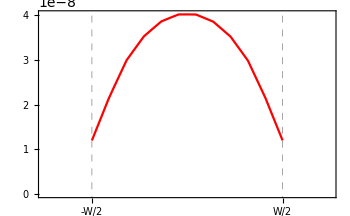
-Graphics3D- | -Graphics-

```mathematica
Block[{bOut,bOutInterpolation,file,sdp,lp},
file=FileNameJoin[{FileNameDrop[Directory[],-1],"out-files","accumulated_000--A.h5"}];
bOut=Import[file,{"Data","/Bo_acc"}];
bOutInterpolation=ElementMeshInterpolation[{mesh["SO3"]["cube-periodic"]},velocities["SO3"][[All,1]].bOut,"ExtrapolationHandler"->{Function[Indeterminate]}];

sdp=Show[
SliceDensityPlot3D[bOutInterpolation[x,y,z],"CenterPlanes",{x,y,z}∈mesh["SO3"]["cube-periodic"],ColorFunction->"TemperatureMap",AxesLabel->{x,y,z},BoxRatios->Automatic,Boxed->False,Axes->False,ImageSize->350],
Graphics3D[{
{Opacity[0.5],Red,InfinitePlane[{{0,1,0},{0,0,1},{0,1,1}}]}}]
];

lp=Plot[bOutInterpolation[0,y,0],{y,-750,750},PlotRange->{{-750,750},{0,Automatic}},PlotStyle->Red,Frame->True,LabelStyle->Directive[Black,16],ImageSize->350,FrameTicks->{{None,None},{{{-500,"-W/2"},{500,"W/2"}},None}},GridLines->{{-500,500},None},GridLinesStyle->Directive[Dashed,Gray]];

Multicolumn[{sdp,lp},2]

]
```